### A message

```mathematica
msg="she sells sea shells by the sea shore";
```

### break up the message into characters.

```mathematica
chars=Characters[msg]
```

{s,h,e, ,s,e,l,l,s, ,s,e,a, ,s,h,e,l,l,s, ,b,y, ,t,h,e, ,s,e,a, ,s,h,o,r,e}

### eliminates duplicates

```mathematica
alphabet=Union[chars]
```

{ ,a,b,e,h,l,o,r,s,t,y}

### Here are all 4-bit binary integers between 1 and 11.

```mathematica
fcodes=Table[IntegerDigits[i,2,4],{i,11}]
```

{{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1}}

### Convert the codes to a set of rules.

```mathematica
InputForm[frules=Thread[alphabet->fcodes]](*这里对结果命名，以便后续使用*)
```

{" " -> {0, 0, 0, 1}, "a" -> {0, 0, 1, 0}, "b" -> {0, 0, 1, 1}, 
 "e" -> {0, 1, 0, 0}, "h" -> {0, 1, 0, 1}, "l" -> {0, 1, 1, 0}, 
 "o" -> {0, 1, 1, 1}, "r" -> {1, 0, 0, 0}, "s" -> {1, 0, 0, 1}, 
 "t" -> {1, 0, 1, 0}, "y" -> {1, 0, 1, 1}}

### embed the rules in a function called fixedCode.

```mathematica
fixedCode[c_String]:=c/.frules
```

```mathematica
TableForm[{InputForm[#],{fixedCode[#]}}&/@alphabet]
```

" " | 0 | 0 | 0 | 1
"a" | 0 | 0 | 1 | 0
"b" | 0 | 0 | 1 | 1
"e" | 0 | 1 | 0 | 0
"h" | 0 | 1 | 0 | 1
"l" | 0 | 1 | 1 | 0
"o" | 0 | 1 | 1 | 1
"r" | 1 | 0 | 0 | 0
"s" | 1 | 0 | 0 | 1
"t" | 1 | 0 | 1 | 0
"y" | 1 | 0 | 1 | 1

```mathematica
encode[code_,msg_]:=Flatten[code/@Characters[msg]]
```

```mathematica
encode[fixedCode,msg]
```

{1,0,0,1,0,1,0,1,0,1,0,0,0,0,0,1,1,0,0,1,0,1,0,0,0,1,1,0,0,1,1,0,1,0,0,1,0,0,0,1,1,0,0,1,0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,1,0,1,0,1,0,1,0,0,0,1,1,0,0,1,1,0,1,0,0,1,0,0,0,1,0,0,1,1,1,0,1,1,0,0,0,1,1,0,1,0,0,1,0,1,0,1,0,0,0,0,0,1,1,0,0,1,0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,1,0,1,0,1,0,1,1,1,1,0,0,0,0,1,0,0}

```mathematica
Length[%]
```

148

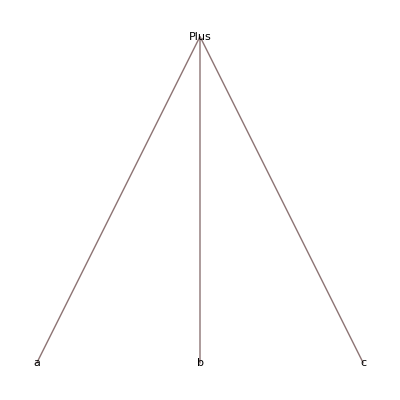

```mathematica
TreeForm[Plus[a+b+c]]
```

```mathematica
Plus[a+b+c][[{1}]]
```

a

### Constructing a Huffman code

```mathematica
pool={Count[chars,#],#}&/@alphabet
```

{{7, },{2,a},{1,b},{7,e},{4,h},{4,l},{1,o},{1,r},{8,s},{1,t},{1,y}}

```mathematica
pool=Sort[pool]
```

{{1,b},{1,o},{1,r},{1,t},{1,y},{2,a},{4,h},{4,l},{7, },{7,e},{8,s}}

```mathematica
Take[pool,2]
```

{{1,b},{1,o}}

```mathematica
Transpose[%]
```

{{1,1},{b,o}}

```mathematica
MapAt[Plus@@#&,%,{1}]
```

{2,{b,o}}

### the combine function

```mathematica
combine[x_]:=If[Length[x]<2,x,Union[Drop[x,2],{MapAt[Plus@@#&,Transpose[Take[x,2]],{1}]}]]
```

```mathematica
pool=combine[pool]
```

{{1,r},{1,t},{1,y},{2,a},{2,{b,o}},{4,h},{4,l},{7, },{7,e},{8,s}}

```mathematica
pool=combine[pool]
```

{{1,y},{2,a},{2,{b,o}},{2,{r,t}},{4,h},{4,l},{7, },{7,e},{8,s}}

### use FixedPoint to iterate this

```mathematica
FixedPoint[combine,pool]
```

{{37,{{{{y,a},h},s},{{l,{{b,o},{r,t}}},{ ,e}}}}}

### use the combine function we get a tree

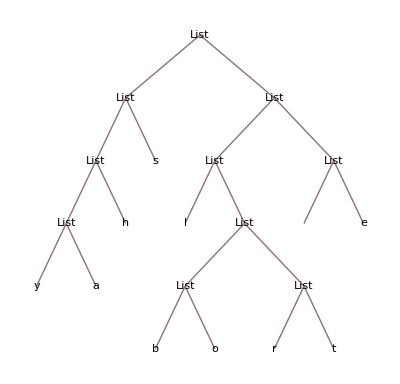

```mathematica
TreeForm[tree=%[[1,2]]]
```

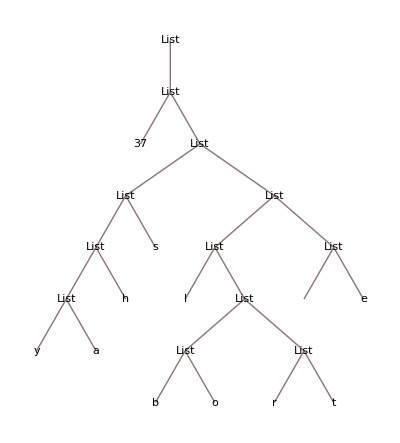

```mathematica
TreeForm[%105]
```

### now we get the function variableCode

```mathematica
variableCode[c_String]:=Position[tree,c][[1]]-1
```

### Decoding a coded message

```mathematica
code2char[t_List,c_List]:=Extract[t,c+1]
```

### a finite state machine

```mathematica
trans[state_List,input_Integer]:=With[{newstate=Append[state,input]},
If[StringQ[code2char[tree,newstate]],decoded=decoded<>code2char[tree,newstate];{},
newstate]
]
```

```mathematica
decoded="";
FoldList[trans,{},{0,1,0,0,1,1,1,1,1}]
```

{{},{0},{},{0},{0,0},{},{1},{1,1},{},{1}}

```mathematica
decoded
```

she

```mathematica
FoldList[f,{},{0,1,0,0,1,1,1,1,1}]
```

{{},f[{},0],f[f[{},0],1],f[f[f[{},0],1],0],f[f[f[f[{},0],1],0],0],f[f[f[f[f[{},0],1],0],0],1],f[f[f[f[f[f[{},0],1],0],0],1],1],f[f[f[f[f[f[f[{},0],1],0],0],1],1],1],f[f[f[f[f[f[f[f[{},0],1],0],0],1],1],1],1],f[f[f[f[f[f[f[f[f[{},0],1],0],0],1],1],1],1],1]}

```mathematica
Short[encodedText=encode[variableCode,msg]]
```

{0,1,0,0,1,1,1,1,1,1,0,0,1,1,1,1,1,0,0,«76»,0,0,1,0,0,1,1,0,1,0,1,1,0,1,1,0,1,1,1}

```mathematica
Length[encodedText]
```

114

```mathematica
decoded="";
Fold[trans,{},encodedText]
```

{}

```mathematica
decoded
```

she sells sea shells by the sea shore

### a new version trans without global variable

```mathematica
Clear[trans]
trans[code_List,input_Integer]:=
With[{string=code[[1]],
list=Append[code[[2]],input]
},
If[StringQ[code2char[tree,list]],
{string<>code2char[tree,list],{}},
{string,list}]
]
```

### now test it

```mathematica
FoldList[trans,{"",{}},{0,1,0,0,1,1,1,1,1}]//InputForm
```

{{"", {}}, {"", {0}}, {"s", {}}, {"s", {0}}, {"s", {0, 0}}, {"sh", {}}, 
 {"sh", {1}}, {"sh", {1, 1}}, {"she", {}}, {"she", {1}}}

### The complete decoding routine is shown below.

```mathematica
huffmanDecode[tr_List,input_List]:=Block[{tree=tr},Fold[trans,{"",{}},input][[1]]]
```

```mathematica
huffmanDecode[tree,encodedText]
```

she sells sea shells by the sea shore

### Embedding the code tree in the transition function

```mathematica
Clear[trans]
trans[tr_List]:=Function[{code,input},
With[{string=code[[1]],codeList=Append[code[[2]],input]},
If[StringQ[code2char[tr,codeList]],
{string<>code2char[tr,codeList],{}},
{string,codeList}]]
]
```

### test the embedded function

```mathematica
Clear[huffmanDecode]
huffmanDecode[tr_List,input_List]:=
Fold[trans[tr],{"",{}},input][[1]]
```

```mathematica
someOtherTree=tree;
Clear[tree]
huffmanDecode[someOtherTree,encodedText]
```

she sells sea shells by the sea shore

```mathematica
someOtherTree
```

{{{{y,a},h},s},{{l,{{b,o},{r,t}}},{ ,e}}}